```mathematica
Plot3D[(2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z-d)^2]-1/Sqrt[r^2+(z+d)^2])/d^2/.{d->0.00005},{z,-0.0005,0.0005},{r,-0.0005,0.0005},PlotRange->{-200/0.00005^2,200/0.00005^2}]
```

-Graphics3D-

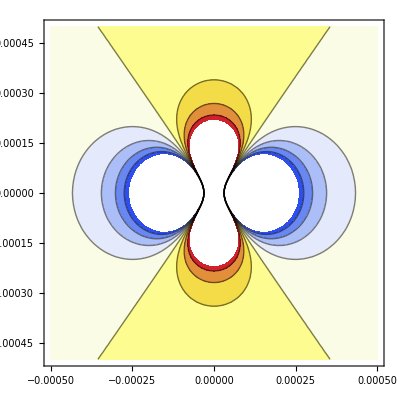

```mathematica
ContourPlot[(2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z-d)^2]-1/Sqrt[r^2+(z+d)^2])/d^2/.{d->0.00005},{z,-0.0005,0.0005},{r,-0.0005,0.0005},ColorFunction->"TemperatureMap"]
```

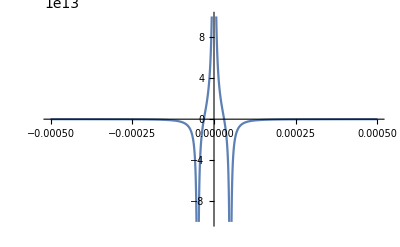

```mathematica
Plot[(2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z-d)^2]-1/Sqrt[r^2+(z+d)^2])/d^2/.{r->0,d->0.00005},{z,-0.0005,0.0005},PlotRange->{-10^14,10^14}]
```

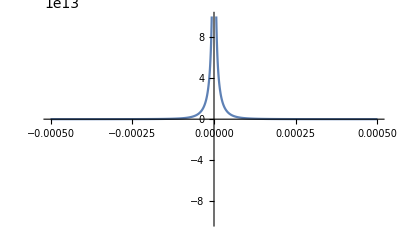

```mathematica
Plot[(2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z-d)^2]-1/Sqrt[r^2+(z+d)^2])/d^2/.{z->0,d->0.00005},{r,-0.0005,0.0005},PlotRange->{-10^14,10^14}]
```

```mathematica
D[D[-1/Sqrt[r^2+z^2],z],z]
```

-(3 z^2)/((r^2+z^2)^(5/2))+1/((r^2+z^2)^(3/2))

```mathematica
Plot3D[-(3 z^2)/((r^2+z^2)^(5/2))+1/((r^2+z^2)^(3/2)),{z,-0.0005,0.0005},{r,-0.0005,0.0005}]
```

-Graphics3D-

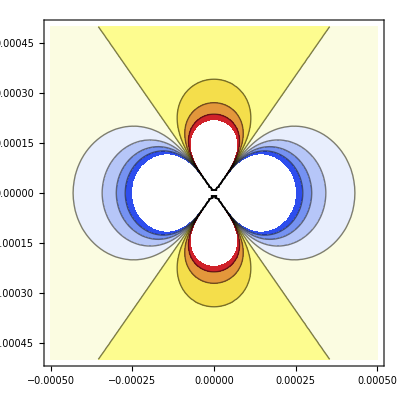

```mathematica
ContourPlot[-(3 z^2)/((r^2+z^2)^(5/2))+1/((r^2+z^2)^(3/2)),{z,-0.0005,0.0005},{r,-0.0005,0.0005},ColorFunction->"TemperatureMap"]
```

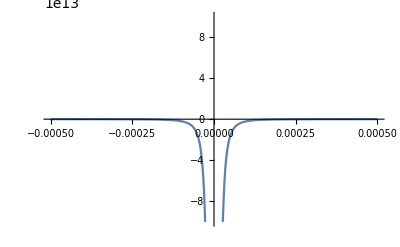

```mathematica
Plot[-(3 z^2)/((r^2+z^2)^(5/2))+1/((r^2+z^2)^(3/2))/.{r->0},{z,-0.0005,0.0005},PlotRange->{-10^14,10^14}]
```

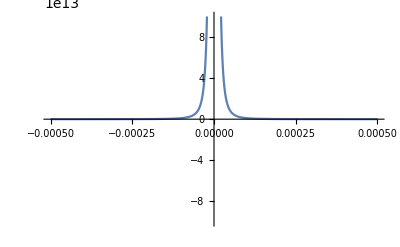

```mathematica
Plot[-(3 z^2)/((r^2+z^2)^(5/2))+1/((r^2+z^2)^(3/2))/.{z->0},{r,-0.0005,0.0005},PlotRange->{-10^14,10^14}]
```

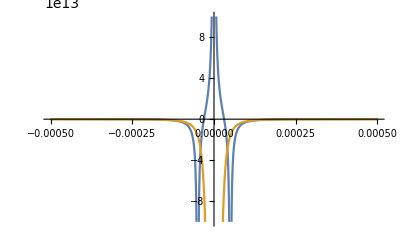

```mathematica
Plot[{(2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z-d)^2]-1/Sqrt[r^2+(z+d)^2])/d^2/.{r->0,d->0.00005},-(3 z^2)/((r^2+z^2)^(5/2))+1/((r^2+z^2)^(3/2))/.{r->0,d->0.00005}},{z,-0.0005,0.0005},PlotRange->{-10^14,10^14}]
```

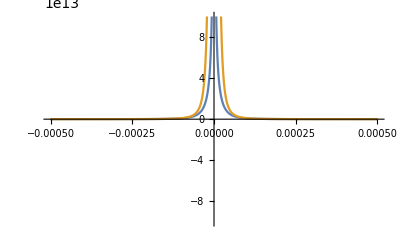

```mathematica
Plot[{(2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z-d)^2]-1/Sqrt[r^2+(z+d)^2])/d^2/.{z->0,d->0.00005},-(3 z^2)/((r^2+z^2)^(5/2))+1/((r^2+z^2)^(3/2))/.{z->0,d->0.00005}},{r,-0.0005,0.0005},PlotRange->{-10^14,10^14}]
```

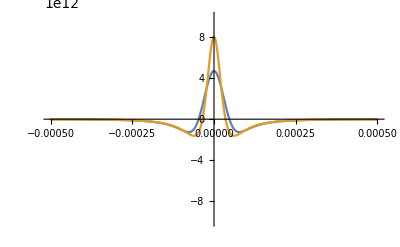

```mathematica
Plot[{(2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z-d)^2]-1/Sqrt[r^2+(z+d)^2])/d^2/.{r->0.00005,d->0.00005},-(3 z^2)/((r^2+z^2)^(5/2))+1/((r^2+z^2)^(3/2))/.{r->0.00005,d->0.00005}},{z,-0.0005,0.0005},PlotRange->{-10^13,10^13}]
```

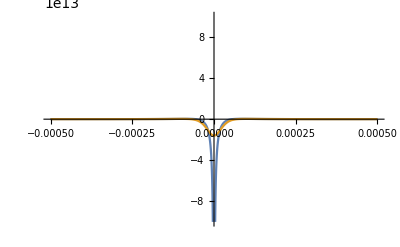

```mathematica
Plot[{(2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z-d)^2]-1/Sqrt[r^2+(z+d)^2])/d^2/.{z->0.00005,d->0.00005},-(3 z^2)/((r^2+z^2)^(5/2))+1/((r^2+z^2)^(3/2))/.{z->0.00005,d->0.00005}},{r,-0.0005,0.0005},PlotRange->{-10^14,10^14}]
```

```mathematica
D[D[-1/Sqrt[r^2+z^2],r],r]+D[-1/Sqrt[r^2+z^2],r]/r+D[D[-1/Sqrt[r^2+z^2],z],z]
```

-(3 r^2)/((r^2+z^2)^(5/2))-(3 z^2)/((r^2+z^2)^(5/2))+3/((r^2+z^2)^(3/2))

```mathematica
FullSimplify[-(3 r^2)/((r^2+z^2)^(5/2))-(3 z^2)/((r^2+z^2)^(5/2))+3/((r^2+z^2)^(3/2))]
```

0

```mathematica
Solve[(2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z-d)^2]-1/Sqrt[r^2+(z+d)^2])/d^2==0/.{r->0},z]
```

{{z→1/2 (d-√5 d)},{z→1/2 (-d+√5 d)}}

```mathematica
FullSimplify[1/2 (-d+√5 d)]
```

1/2 (-1+√5) d

```mathematica
Solve[-(3 z^2)/((r^2+z^2)^(5/2))+1/((r^2+z^2)^(3/2))==0,z]
```

{{z→-r/(√2)},{z→r/(√2)}}

```mathematica
Integrate[2*Pi*r*(2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z-d)^2]-1/Sqrt[r^2+(z+d)^2])/d^2,{r,0,Infinity}]
```

(2 π (√((d-z)^2)-2 √(z^2)+√((d+z)^2)))/d^2

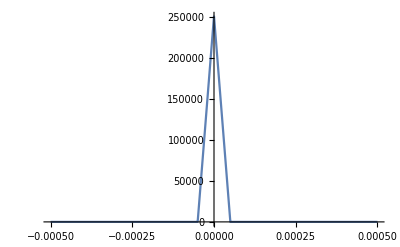

```mathematica
Plot[(2 π (√((d-z)^2)-2 √(z^2)+√((d+z)^2)))/d^2/.{d->0.00005},{z,-0.0005,0.0005},PlotRange->All]
```

```mathematica
Integrate[Exp[-(r/w)^2/2]2*Pi*r*(2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z-d)^2]-1/Sqrt[r^2+(z+d)^2])/d^2,{r,0,Infinity},Assumptions->{d>0,w>0}]
```

ConditionalExpression[(√2 π^(3/2) w (-ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2)+2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2)-ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2)+ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2) Erf[1/(√2 w √(1/(d-z)^2))]-2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2) Erf[1/(√2 w √(1/z^2))]+ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2) Erf[1/(√2 w √(1/(d+z)^2))]))/d^2, ]

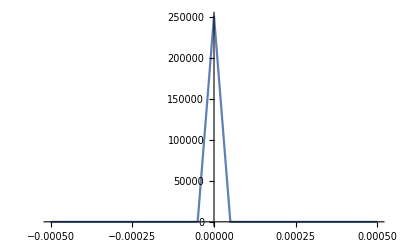

```mathematica
Plot[1/d^2 √2 π^(3/2) w (-ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2)+2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2)-ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2)+ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2) Erf[1/(√2 w √(1/(d-z)^2))]-2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2) Erf[1/(√2 w √(1/z^2))]+ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2) Erf[1/(√2 w √(1/(d+z)^2))])/.{d->0.00005,w->0.1},{z,-0.0005,0.0005},PlotRange->All]
```

```mathematica
Limit[1/d^2 √2 π^(3/2) w (-ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2)+2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2)-ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2)+ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2) Erf[1/(√2 w √(1/(d-z)^2))]-2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2) Erf[1/(√2 w √(1/z^2))]+ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2) Erf[1/(√2 w √(1/(d+z)^2))]),z->0]
```

-(2 √2 π^(3/2) w (d (-1+√(1/d^2) √(d^2) ⅇ^(d^2/(2 w^2)))-√(d^2) ⅇ^(d^2/(2 w^2)) Erf[d/(√2 w)]))/d^3

```mathematica
FullSimplify[-(2 √2 π^(3/2) w (d (-1+√(1/d^2) √(d^2) ⅇ^(d^2/(2 w^2)))-√(d^2) ⅇ^(d^2/(2 w^2)) Erf[d/(√2 w)]))/d^3,Assumptions->{d>0,w>0}]
```

-(2 √2 π^(3/2) w (-1+ⅇ^(d^2/(2 w^2)) Erfc[d/(√2 w)]))/d^2

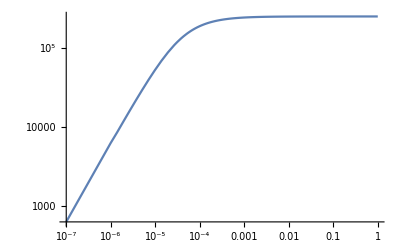

```mathematica
LogLogPlot[-(2 √2 π^(3/2) w (-1+ⅇ^(d^2/(2 w^2)) Erfc[d/(√2 w)]))/d^2/.{d->0.00005},{w,10^-7,1}]
```

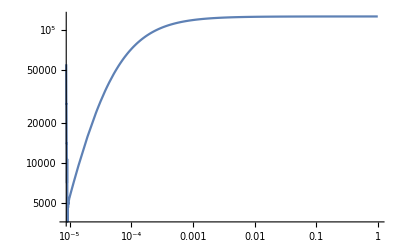

```mathematica
LogLogPlot[1/d^2 √2 π^(3/2) w (-ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2)+2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2)-ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2)+ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2) Erf[1/(√2 w √(1/(d-z)^2))]-2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2) Erf[1/(√2 w √(1/z^2))]+ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2) Erf[1/(√2 w √(1/(d+z)^2))])/.{d->0.00005,z->0.000025},{w,10^-7,1},PlotRange->All]
```

```mathematica
FullSimplify[1/d^2 √2 π^(3/2) w (-ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2)+2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2)-ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2)+ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2) Erf[1/(√2 w √(1/(d-z)^2))]-2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2) Erf[1/(√2 w √(1/z^2))]+ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2) Erf[1/(√2 w √(1/(d+z)^2))])/.z->d/2]
```

-(√2 ⅇ^(d^2/(8 w^2)) π^(3/2) w (√(1/d^2) d (-1+ⅇ^(d^2/w^2))+Erf[d/(2 √2 w)]-ⅇ^(d^2/w^2) Erf[(3 d)/(2 √2 w)]))/(d √(d^2))

```mathematica
FullSimplify[-(√2 ⅇ^(d^2/(8 w^2)) π^(3/2) w (√(1/d^2) d (-1+ⅇ^(d^2/w^2))+Erf[d/(2 √2 w)]-ⅇ^(d^2/w^2) Erf[(3 d)/(2 √2 w)]))/(d √(d^2)),Assumptions->{d>0,w>0}]
```

-(√2 ⅇ^(d^2/(8 w^2)) π^(3/2) w (-1+Erf[d/(2 √2 w)]+ⅇ^(d^2/w^2) Erfc[(3 d)/(2 √2 w)]))/d^2

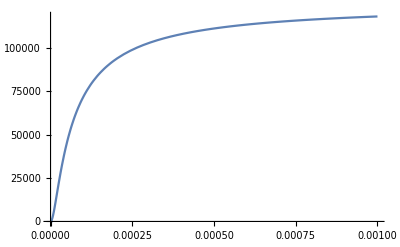

```mathematica
Plot[-(√2 ⅇ^(d^2/(8 w^2)) π^(3/2) w (-1+Erf[d/(2 √2 w)]+ⅇ^(d^2/w^2) Erfc[(3 d)/(2 √2 w)]))/d^2/.{d->0.00005},{w,0,0.001},PlotRange->All]
```

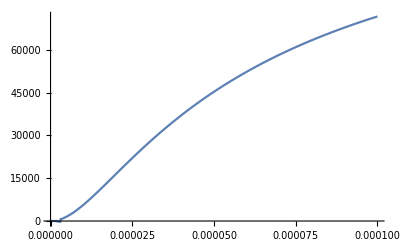

```mathematica
Plot[-(√2 ⅇ^(d^2/(8 w^2)) π^(3/2) w (-1+Erf[d/(2 √2 w)]+ⅇ^(d^2/w^2) Erfc[(3 d)/(2 √2 w)]))/d^2/.{d->0.00005},{w,0,0.0001},PlotRange->All]
```

```mathematica
FullSimplify[1/d^2 √2 π^(3/2) w (-ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2)+2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2)-ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2)+ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2) Erf[1/(√2 w √(1/(d-z)^2))]-2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2) Erf[1/(√2 w √(1/z^2))]+ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2) Erf[1/(√2 w √(1/(d+z)^2))])/.z->2*d]
```

-(√2 √(1/d^2) ⅇ^(d^2/(2 w^2)) π^(3/2) w (Erfc[1/(√2 √(1/d^2) w)]+ⅇ^((4 d^2)/w^2) Erfc[3/(√2 √(1/d^2) w)]-2 ⅇ^((3 d^2)/(2 w^2)) Erfc[(√2)/(√(1/d^2) w)]))/(√(d^2))

```mathematica
FullSimplify[-(√2 √(1/d^2) ⅇ^(d^2/(2 w^2)) π^(3/2) w (Erfc[1/(√2 √(1/d^2) w)]+ⅇ^((4 d^2)/w^2) Erfc[3/(√2 √(1/d^2) w)]-2 ⅇ^((3 d^2)/(2 w^2)) Erfc[(√2)/(√(1/d^2) w)]))/(√(d^2)),Assumptions->{d>0,w>0}]
```

-(√2 ⅇ^(d^2/(2 w^2)) π^(3/2) w (Erfc[d/(√2 w)]+ⅇ^((4 d^2)/w^2) Erfc[(3 d)/(√2 w)]-2 ⅇ^((3 d^2)/(2 w^2)) Erfc[(√2 d)/w]))/d^2

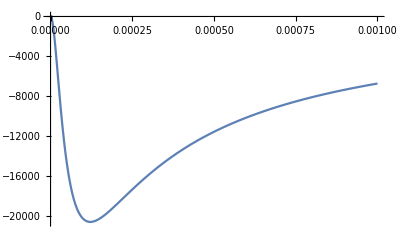

```mathematica
Plot[-(√2 ⅇ^(d^2/(2 w^2)) π^(3/2) w (Erfc[d/(√2 w)]+ⅇ^((4 d^2)/w^2) Erfc[(3 d)/(√2 w)]-2 ⅇ^((3 d^2)/(2 w^2)) Erfc[(√2 d)/w]))/d^2/.{d->0.00005},{w,0,0.001},PlotRange->All]
```

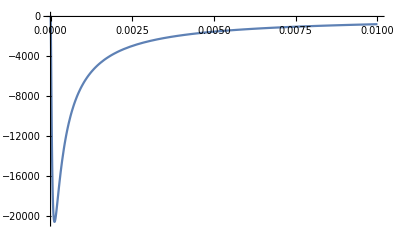

```mathematica
Plot[-(√2 ⅇ^(d^2/(2 w^2)) π^(3/2) w (Erfc[d/(√2 w)]+ⅇ^((4 d^2)/w^2) Erfc[(3 d)/(√2 w)]-2 ⅇ^((3 d^2)/(2 w^2)) Erfc[(√2 d)/w]))/d^2/.{d->0.00005},{w,0,0.01},PlotRange->All]
```

```mathematica
FullSimplify[1/d^2 √2 π^(3/2) w (-ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2)+2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2)-ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2)+ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2) Erf[1/(√2 w √(1/(d-z)^2))]-2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2) Erf[1/(√2 w √(1/z^2))]+ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2) Erf[1/(√2 w √(1/(d+z)^2))])/.z->10*d]
```

-(√2 √(1/d^2) ⅇ^((81 d^2)/(2 w^2)) π^(3/2) w (Erfc[9/(√2 √(1/d^2) w)]+ⅇ^((20 d^2)/w^2) Erfc[11/(√2 √(1/d^2) w)]-2 ⅇ^((19 d^2)/(2 w^2)) Erfc[(5 √2)/(√(1/d^2) w)]))/(√(d^2))

```mathematica
FullSimplify[-(√2 √(1/d^2) ⅇ^((81 d^2)/(2 w^2)) π^(3/2) w (Erfc[9/(√2 √(1/d^2) w)]+ⅇ^((20 d^2)/w^2) Erfc[11/(√2 √(1/d^2) w)]-2 ⅇ^((19 d^2)/(2 w^2)) Erfc[(5 √2)/(√(1/d^2) w)]))/(√(d^2)),Assumptions->{d>0,w>0}]
```

-(√2 ⅇ^((81 d^2)/(2 w^2)) π^(3/2) w (Erfc[(9 d)/(√2 w)]+ⅇ^((20 d^2)/w^2) Erfc[(11 d)/(√2 w)]-2 ⅇ^((19 d^2)/(2 w^2)) Erfc[(5 √2 d)/w]))/d^2

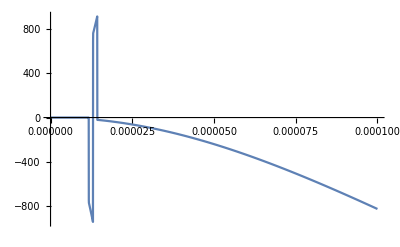

```mathematica
Plot[-(√2 ⅇ^((81 d^2)/(2 w^2)) π^(3/2) w (Erfc[(9 d)/(√2 w)]+ⅇ^((20 d^2)/w^2) Erfc[(11 d)/(√2 w)]-2 ⅇ^((19 d^2)/(2 w^2)) Erfc[(5 √2 d)/w]))/d^2/.{d->0.00005},{w,0,0.0001},PlotRange->All]
```

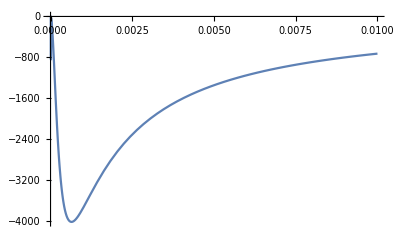

```mathematica
Plot[-(√2 ⅇ^((81 d^2)/(2 w^2)) π^(3/2) w (Erfc[(9 d)/(√2 w)]+ⅇ^((20 d^2)/w^2) Erfc[(11 d)/(√2 w)]-2 ⅇ^((19 d^2)/(2 w^2)) Erfc[(5 √2 d)/w]))/d^2/.{d->0.00005},{w,0,0.01},PlotRange->All]
```

```mathematica
FullSimplify[1/d^2 √2 π^(3/2) w (-ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2)+2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2)-ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2)+ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2) Erf[1/(√2 w √(1/(d-z)^2))]-2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2) Erf[1/(√2 w √(1/z^2))]+ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2) Erf[1/(√2 w √(1/(d+z)^2))])/.z->1.1*d]
```

(√(1/d^2) w (ⅇ^((0.005 d^2)/w^2) (-7.8748+7.8748 Erf[0.0707107/(√(1/d^2) w)])+ⅇ^((0.605 d^2)/w^2) (15.7496-15.7496 Erf[0.777817/(√(1/d^2) w)])+ⅇ^((2.205 d^2)/w^2) (-7.8748+7.8748 Erf[1.48492/(√(1/d^2) w)])))/(√(d^2))

```mathematica
FullSimplify[1/(√(d^2))√(1/d^2) w (ⅇ^((0.005000000000000009 d^2)/w^2) (-7.8748049728612095+7.8748049728612095 Erf[0.07071067811865481/(√(1/d^2) w)])+ⅇ^((0.6050000000000001 d^2)/w^2) (15.749609945722419-15.749609945722419 Erf[0.7778174593052023/(√(1/d^2) w)])+ⅇ^((2.205 d^2)/w^2) (-7.8748049728612095+7.8748049728612095 Erf[1.4849242404917498/(√(1/d^2) w)])),Assumptions->{d>0,w>0}]
```

(w (ⅇ^((0.005 d^2)/w^2) (-7.8748+7.8748 Erf[(0.0707107 d)/w])+ⅇ^((0.605 d^2)/w^2) (15.7496-15.7496 Erf[(0.777817 d)/w])+ⅇ^((2.205 d^2)/w^2) (-7.8748+7.8748 Erf[(1.48492 d)/w])))/d^2

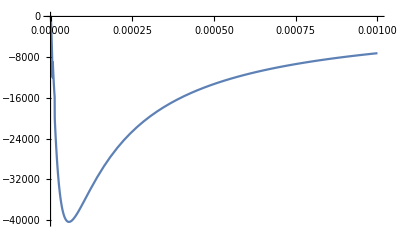

```mathematica
Plot[1/d^2 w (ⅇ^((0.005000000000000009 d^2)/w^2) (-7.8748049728612095+7.8748049728612095 Erf[(0.07071067811865481 d)/w])+ⅇ^((0.6050000000000001 d^2)/w^2) (15.749609945722419-15.749609945722419 Erf[(0.7778174593052023 d)/w])+ⅇ^((2.205 d^2)/w^2) (-7.8748049728612095+7.8748049728612095 Erf[(1.4849242404917498 d)/w]))/.{d->0.00005},{w,0,0.001},PlotRange->All]
```

```mathematica
FullSimplify[1/d^2 √2 π^(3/2) w (-ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2)+2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2)-ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2)+ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2) Erf[1/(√2 w √(1/(d-z)^2))]-2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2) Erf[1/(√2 w √(1/z^2))]+ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2) Erf[1/(√2 w √(1/(d+z)^2))])/.z->0.9*d]
```

(√(1/d^2) w (ⅇ^((0.005 d^2)/w^2) (-7.8748+7.8748 Erf[0.0707107/(√(1/d^2) w)])+ⅇ^((0.405 d^2)/w^2) (15.7496-15.7496 Erf[0.636396/(√(1/d^2) w)])+ⅇ^((1.805 d^2)/w^2) (-7.8748+7.8748 Erf[1.3435/(√(1/d^2) w)])))/(√(d^2))

```mathematica
FullSimplify[1/(√(d^2))√(1/d^2) w (ⅇ^((0.0049999999999999975 d^2)/w^2) (-7.87480497286121+7.87480497286121 Erf[0.07071067811865472/(√(1/d^2) w)])+ⅇ^((0.405 d^2)/w^2) (15.749609945722417-15.749609945722417 Erf[0.6363961030678926/(√(1/d^2) w)])+ⅇ^((1.805 d^2)/w^2) (-7.874804972861208+7.874804972861208 Erf[1.3435028842544403/(√(1/d^2) w)])),Assumptions->{d>0,w>0}]
```

(w (ⅇ^((0.005 d^2)/w^2) (-7.8748+7.8748 Erf[(0.0707107 d)/w])+ⅇ^((0.405 d^2)/w^2) (15.7496-15.7496 Erf[(0.636396 d)/w])+ⅇ^((1.805 d^2)/w^2) (-7.8748+7.8748 Erf[(1.3435 d)/w])))/d^2

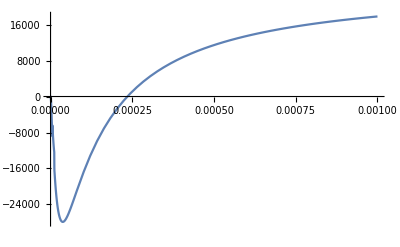

```mathematica
Plot[1/d^2 w (ⅇ^((0.0049999999999999975 d^2)/w^2) (-7.87480497286121+7.87480497286121 Erf[(0.07071067811865472 d)/w])+ⅇ^((0.405 d^2)/w^2) (15.749609945722417-15.749609945722417 Erf[(0.6363961030678926 d)/w])+ⅇ^((1.805 d^2)/w^2) (-7.874804972861208+7.874804972861208 Erf[(1.3435028842544403 d)/w]))/.{d->0.00005},{w,0,0.001},PlotRange->All]
```

```mathematica
FullSimplify[1/d^2 √2 π^(3/2) w (-ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2)+2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2)-ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2)+ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2) Erf[1/(√2 w √(1/(d-z)^2))]-2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2) Erf[1/(√2 w √(1/z^2))]+ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2) Erf[1/(√2 w √(1/(d+z)^2))]),Assumptions->{d>0,z>0,w>0}]
```

-(√2 π^(3/2) w (-2 ⅇ^(z^2/(2 w^2)) Erfc[z/(√2 w)]+ⅇ^((d+z)^2/(2 w^2)) Erfc[(d+z)/(√2 w)]+ⅇ^((d-z)^2/(2 w^2)) Erfc[Abs[d-z]/(√2 w)]))/d^2

```mathematica
Plot3D[-(√2 π^(3/2) w (-2 ⅇ^(z^2/(2 w^2)) Erfc[z/(√2 w)]+ⅇ^((d+z)^2/(2 w^2)) Erfc[(d+z)/(√2 w)]+ⅇ^((d-z)^2/(2 w^2)) Erfc[Abs[d-z]/(√2 w)]))/d^2]
```

```mathematica
-(√2 π^(3/2)  (-2 ⅇ^(zn^2/2) Erfc[zn/(√2)]+ⅇ^((dn+zn)^2/2) Erfc[(dn+zn)/(√2)]+ⅇ^((dn-zn)^2/2) Erfc[Abs[dn-zn]/(√2)]))/dn
```

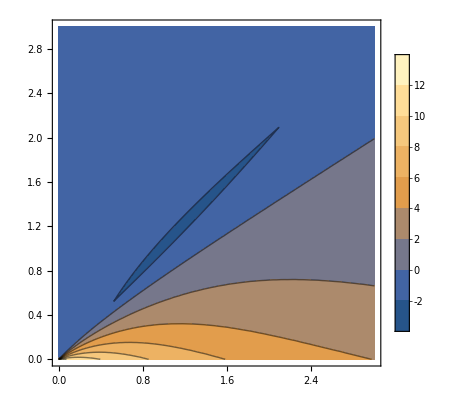

```mathematica
ContourPlot[-(√2 π^(3/2)  (-2 ⅇ^(zn^2/2) Erfc[zn/(√2)]+ⅇ^((dn+zn)^2/2) Erfc[(dn+zn)/(√2)]+ⅇ^((dn-zn)^2/2) Erfc[Abs[dn-zn]/(√2)]))/dn,{dn,0,3},{zn,0,3},PlotRange->All,PlotLegends->Automatic]
```

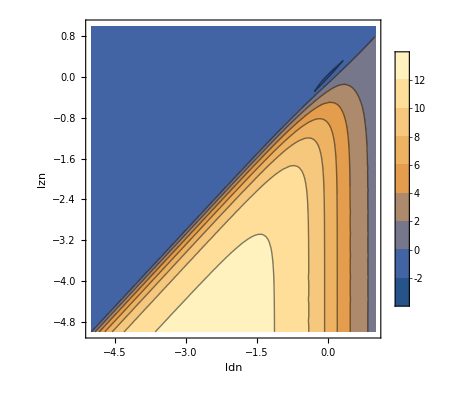

```mathematica
ContourPlot[-(√2 π^(3/2)  (-2 ⅇ^(zn^2/2) Erfc[zn/(√2)]+ⅇ^((dn+zn)^2/2) Erfc[(dn+zn)/(√2)]+ⅇ^((dn-zn)^2/2) Erfc[Abs[dn-zn]/(√2)]))/dn/.{dn->Exp[Log[10]*ldn],zn->Exp[Log[10]*lzn]},{ldn,-5,1},{lzn,-5,1},PlotRange->All,PlotLegends->Automatic,FrameLabel->{"ldn","lzn","abc"}]
```

```mathematica
Exp[1*Log[10]]
```

10

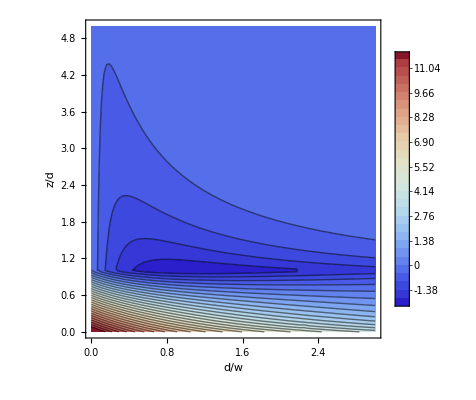

```mathematica
ContourPlot[-(√2 π^(3/2)  (-2 ⅇ^((z2d*dn)^2/2) Erfc[(dn*z2d)/(√2)]+ⅇ^((dn(1+z2d))^2/2) Erfc[(dn(1+z2d))/(√2)]+ⅇ^((dn(1-z2d))^2/2) Erfc[Abs[(dn(1-z2d))]/(√2)]))/dn,{dn,0,3},{z2d,0,5},PlotRange->All,PlotLegends->Automatic,FrameLabel->{"d/w","z/d","abc"},Contours->30,ColorFunction->"ThermometerColors",PlotRange->{-5,5}]
```

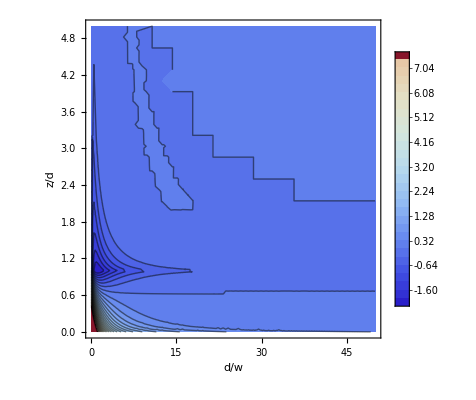

```mathematica
ContourPlot[-(√2 π^(3/2)  (-2 ⅇ^((z2d*dn)^2/2) Erfc[(dn*z2d)/(√2)]+ⅇ^((dn(1+z2d))^2/2) Erfc[(dn(1+z2d))/(√2)]+ⅇ^((dn(1-z2d))^2/2) Erfc[Abs[(dn(1-z2d))]/(√2)]))/dn,{dn,0,50},{z2d,0,5},PlotRange->All,PlotLegends->Automatic,FrameLabel->{"d/w","z/d","abc"},Contours->30,ColorFunction->"ThermometerColors",PlotRange->{-5,5}]
```

```mathematica
Plot3D[-(√2 π^(3/2)  (-2 ⅇ^((z2d*dn)^2/2) Erfc[(dn*z2d)/(√2)]+ⅇ^((dn(1+z2d))^2/2) Erfc[(dn(1+z2d))/(√2)]+ⅇ^((dn(1-z2d))^2/2) Erfc[Abs[(dn(1-z2d))]/(√2)]))/dn,{dn,0,10},{z2d,0,3},PlotRange->All,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
Plot3D[-(dn √2 π^(3/2)  (-2 ⅇ^((z2d*dn)^2/2) Erfc[(dn*z2d)/(√2)]+ⅇ^((dn(1+z2d))^2/2) Erfc[(dn(1+z2d))/(√2)]+ⅇ^((dn(1-z2d))^2/2) Erfc[Abs[(dn(1-z2d))]/(√2)]))/dn,{dn,0,10},{z2d,0,3},PlotRange->All,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics3D-